## Strategy 1

### Math

```mathematica
Clear[λ,μ]
P0[ρ_]:=(1-ρ)/(1-ρ^11) (*Stationary Distribution*)
P[ρ_,n_]:=P0[ρ]*ρ^n (*Prob of being in state n*)
PBlock[ρ_]:=P[ρ,10](*Blocking Probability*)
L[ρ_]:=∑_(n=0)^10 n*P[ρ,n](*AVG num of Customers*)
B[ρ_]:= 1-P0[ρ](*AVG num of Cust being Served*)
Lq[ρ_]:=(L[ρ]-B[ρ] )(*Avergae Que Length*)
S[ρ_,λ_]:=L[ρ]/λ(*AVG sojourn time*)
```

### Blocking Prob

```mathematica
PBlock[0.5]
```

0.00048852

#### Collected Data

```mathematica
PBlockS1x ={0,0.6,0.7,0.8,0.9,1.01,1.1,1.2};
PBlockS1y = ConstantArray[0,8] (*stores the blocking prob for ρ={0.1,1.2}*);
PBlockS1y[[1]]=0;
PBlockS1y[[2]]=Mean[{4/112,1/118,0,0,0,0,5/114,0,0,0}];(*ρ=0.6*)
PBlockS1y[[3]]=Mean[{5/138,0,0,1/152,0,0,1/137,0,0,3/132}];(*ρ=0.7*)
PBlockS1y[[4]]=Mean[{6/153,7/136,0,10/156,0,8/176,7/156,2/153,9/150,11/147}];(*ρ=0.8*)
PBlockS1y[[5]]=Mean[{3/199,26/185,24/158,2/173,3/169,11/185,6/182,2/171,16/183,4/174}]; (*ρ=0.9*)
PBlockS1y[[6]]=Mean[{26/190,5/173,14/175,30/194,19/186,6/188,18/191,21/176,19/179,28/189}]; (*ρ=1.01*)
PBlockS1y[[7]]=Mean[{31/207,31/195,28/204,35/185,21/189,33/187,3/219,22/190,24/188,39/191}]; (*ρ=1.1*)
PBlockS1y[[8]]=Mean[{19/206,55/215,35/194,41/217,79/204,42/204,68/199,38/204,58/188,41/182}](*ρ=1.2*);
PBlockS1Data = Transpose[{PBlockS1x,PBlockS1y}];
```

#### Plots

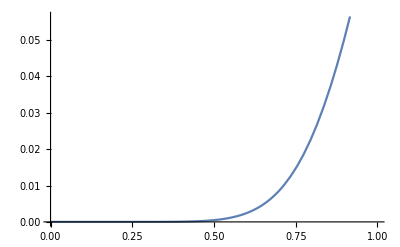

```mathematica
PBlockTherPlot = Plot[{PBlock[ρ]},{ρ,0,1}];

PBlockS1Plot = ListPlot[
PBlockS1Data ,
AxesLabel->{"Load (ρ)","Probability"},
PlotLabel->"Blocking Probability",
PlotStyle->Red,PlotLegends->{"Strat 1"}
];

Show[{PBlockTherPlot}]
```

```mathematica
PBlockTherPlot = Plot[{PBlock[λ]},{λ,0,1}]
```

-Graphics-

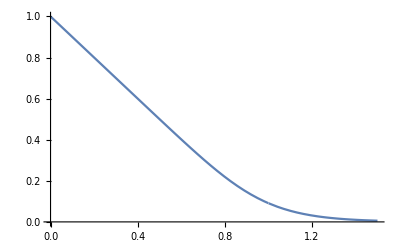

```mathematica
PBlockTherPlot = Plot[{PBlock[1/μ]},{μ,0,1.5}]
```

### Avg Queue Length

```mathematica
QLenS1y[[7]] - Lq[0.6]
QLenS1y[[8]] - Lq[0.7]
QLenS1y[[9]] - Lq[0.8]
QLenS1y[[10]] - Lq[0.9]
```

0.65527

0.699542

0.742246

0.791044

#### Collected Data

```mathematica
QLenS1x ={0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.0};
QLenS1y = ConstantArray[0,11] (*stores the blocking prob for ρ={0.0,1.0}*);
(*μ = 1.0 constant*)
QLenS1y[[1]] = 0; (*ρ=0.0*)
QLenS1y[[2]]=Mean[{0.27926425,0.27892183,0.27794776,0.28487105,0.28262750,0.28282159,0.27939194,0.28061006,0.28629032,0.28098849}];(*ρ=0.1*)
QLenS1y[[3]]=Mean[{0.38109809,0.37091650,0.36873931,0.37602043,0.36673986,0.35571475,0.37139537,0.36274121,0.35630768,0.35799056}];(*ρ=0.2*)
QLenS1y[[4]]=Mean[{0.51368426,0.49589142,0.52432106,0.52033326,0.50403597,0.51674112,0.54833423,0.52051917,0.51715357,0.51776392}];(*ρ=0.3*)
QLenS1y[[5]]=Mean[{0.68367824,0.72532642,0.72494188,0.70538962,0.73603488,0.70223966,0.74186846,0.75372063,0.72725375,0.70280272}];(*ρ=0.4*)
QLenS1y[[6]]=Mean[{0.98856831,1.00212959,1.08348070,1.13571039,1.08743685,1.04664651,1.01321908,1.04438218,1.06046862,1.00426949}]; (*ρ=0.5*)
QLenS1y[[7]]=Mean[{1.79684065,1.44876194,1.52196126,1.51730303,1.45195620,1.57640465,1.50258474,1.58521519,1.40575906,1.35995077}]; (*ρ=0.6*)
QLenS1y[[8]]=Mean[{2.09881240,2.12890494,2.20900243,2.09500061,2.29271337,2.06423732,2.19527843,1.91941401,2.03322653,2.13374476}]; (*ρ=0.7*)
QLenS1y[[9]]=Mean[{3.11369507,2.93603361,2.91307798,2.90445527,2.59299649,2.84377292,3.00553012,2.98619214,3.20018188,2.77761047}]; (*ρ=0.8*)
QLenS1y[[10]]=Mean[{4.08317751,4.01343362,4.02649253,3.58753758,4.13268014,3.83269823,3.59433864,4.19240485,3.70824126,3.89116645}]; (*ρ=0.9*)
QLenS1y[[11]]=Mean[{4.52487749,5.22281887,5.07977078,4.75608697,4.99838721,4.89773452,5.04885959,5.08546625,4.85859170,4.68883900}]; (*ρ=1.0*)

QLenS1Data = Transpose[{QLenS1x,QLenS1y}];
```

#### Plots

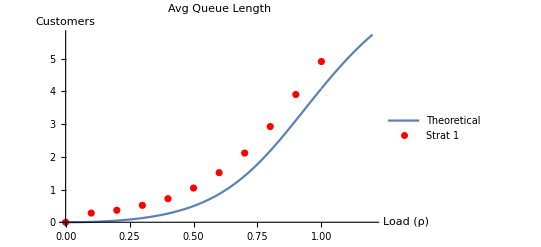

```mathematica
QLenS1TherPlot = Plot[{Lq[ρ]},{ρ,0,1.2},AxesLabel->{"Load (ρ)","Customers"},PlotLabel->"Avg Queue Length",
PlotLegends->{"Theoretical"}];

QLenS1Plot = ListPlot[
QLenS1Data ,
AxesLabel->{"Load (ρ)","Probability"},
PlotLabel->"Blocking Probability",
PlotStyle->Red,PlotLegends->{"Strat 1"}
];

Show[{QLenS1TherPlot,QLenS1Plot}]
```

### Avg Sojourn Time

#### Plots

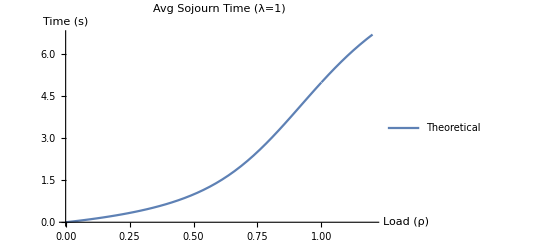

```mathematica
Plot[{S[ρ,1]},{ρ,0,1.2},AxesLabel->{"Load (ρ)","Time (s)"},PlotLabel->"Avg Sojourn Time (λ=1)",
PlotLegends->{"Theoretical"}]
```